## Weighted Fit

```mathematica
data={{0.8412939453125,0.0006787109375000488},{3.228457832336426,0.001987457275390625},{7.180727005004883,0.006916999816894531},{12.689524383982643,0.00041025690734386444},{19.773917039623484,0.0008084890432655811},{28.428132182219997,0.0014104349538683891},{38.652617557672784,0.0022564129903912544},{50.44768833811395,0.003389570862054825},{63.81358461291529,0.004853056278079748},{78.75050342851318,0.006692846305668354},{95.25861514895223,0.008953503333032131},{113.3380695336964,0.011680297087877989},{132.98900753981434,0.014921326655894518},{154.2115601298865,0.01872398378327489},{177.00585263001267,0.02313821972347796},{201.3720079708146,0.02821478503756225},{227.31014622107614,0.034006000962108374},{283.90284618304577,0.04795086523517966},{314.50142759794835,-32.28347865049727},{346.71947693580296,-33.865271157585084},{380.50910288875457,-35.44819264113903},{415.87036471103784,-37.032310613198206},{452.8033205346437,-38.617696549743414},{531.5124529820168,0.12790232826955616},{573.1771208100254,0.1441776598803699},{616.4151616400341,0.16189569421112537},{661.2267199849011,0.18113936972804368},{707.6119473635918,0.20200004219077528},{755.5709999114042,0.22457072837278247},{805.1040396742756,0.24895191960968077},{856.2112368090311,0.2752490902785212},{908.892766552628,0.30357186729088426},{963.1488120803842,0.3340373521205038}};
```

This data is from parallelsperiment_mod -- I just copied over the “final” list.

This cell produces a list from which I can generate a log-log plot. The list is of the form {ln(N), ln(λ), 1/λ Δλ}.

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}];
```

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,14}]*Sum[w[i]*y[i],{i,14}]-Sum[w[i]*x[i],{i,14}]*Sum[w[i]*x[i]*y[i],{i,14}])
```

-0.1036

```mathematica
B=(Sum[w[i],{i,14}]*Sum[w[i]*x[i]*y[i],{i,14}]-Sum[w[i]*x[i],{i,14}]*Sum[w[i]*y[i],{i,14}])/Delta
```

0.930835

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

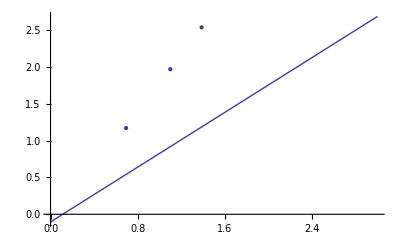

```mathematica
Show[Plot[F[x],{x,0,3}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,33}]]]
```

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,14}]/Delta]
```

0.0000584592

```mathematica
σB=Sqrt[Sum[w[i],{i,14}]/Delta]
```

0.0000319149

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,14}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,14}];
```

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,14}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Hey :(

Making sure nothing stupid happened:

```mathematica
fitvals
```

{-0.221695,1.15931,1.96714,2.54031,2.9849,3.34815,3.65527,3.92132,4.15599,4.3659,4.5558,4.72915,4.88863,5.03628}

```mathematica
Table[loglog[[i,2]],{i,1,14}]
```

{-0.172814,1.172,1.9714,2.54074,2.98432,3.34733,3.65456,3.92087,4.15589,4.3662,4.5565,4.73027,4.89015,5.0382}

Not...that I can see :( :( :(

## Accuracy Check

```mathematica
data
```

{{0.841294,0.000678711},{3.22846,0.00198746},{7.18073,0.006917},{12.6891,0.000410257},{19.7731,0.000808489},{28.4267,0.00141043},{38.6504,0.00225641},{50.4443,0.00338957},{63.8087,0.00485306},{78.7438,0.00669285},{95.2497,0.0089535},{113.326,0.0116803},{132.974,0.0149213},{154.193,0.018724}}

```mathematica
evsfound
```

{{12.9004,13.8672},{19.668,20.6348},{28.3691,29.3359},{39.0039,39.9707},{50.6055,51.5723},{64.1406,65.1074},{78.6426,79.6094},{96.0449,97.0117},{113.447,114.414},{133.75,134.717},{155.02,155.986},{178.223,179.189},{202.393,203.359},{228.496,229.463},{255.566,256.533},{285.537,286.504},{315.508,316.475},{348.379,349.346},{382.217,383.184},{417.988,418.955},{454.727,455.693},{493.398,494.365},{533.037,534.004},{574.609,575.576},{618.115,619.082},{663.555,664.521},{709.961,710.928},{757.334,758.301},{807.607,808.574},{858.848,859.814},{911.055,912.021},{965.195,966.162}}